```mathematica
(*The list I0 contains the forward intensities at fD2O fractions of: 0, 0.1, 0.2, 0.4 0.8,0.9  and 1. List err0 contains the errors. The values are taken from PRIMUS*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
(*calculate I0 at different fractions fD2O*)
```

```mathematica
fD2O=1(*%*);
c=11.9(*mg mL^-1*);
NA=6.02214 10^23(*mol^-1*);
m1=50.685+0.692 fD2O(*kDa*);
m2=11.69+0.191 fD2O(*kDa*);
Δρ1=(2.270-5.643fD2O)10^10 (*cm^-2*);
Δρ2=(6.227-5.403 fD2O)10^10 (*cm^-2*);
v1=0.745(*cm^3 g^-1*);
v2=0.739(*cm^3 g^-1*);
Mw=m1+m2;f1=m1 Mw^-1;f2=m2 Mw^-1;
I0=c Mw/NA (f1 Δρ1 v1+f2 Δρ2 v2)^2
```

0.463951

```mathematica
I0={0.5212,0.3634,0.2221,0.0684,0.1823,0.3204,0.5319}
err0={0.0032,0.0026,0.0024,0.0014,0.0013,0.0014,0.0009}
```

{0.5212,0.3634,0.2221,0.0684,0.1823,0.3204,0.5319}

{0.0032,0.0026,0.0024,0.0014,0.0013,0.0014,0.0009}

```mathematica
(*concentrations used*)
```

```mathematica
c={11.9,11.9,11.9,26.6,11.9,11.9,11.9}
```

{11.9,11.9,11.9,26.6,11.9,11.9,11.9}

```mathematica
(*Calculate the ratio I(0)/c at every fraction fD2O, in units of cm^2 g^-1*)
```

```mathematica
I0c={{0,10^3/c⟦1⟧I0⟦1⟧},{10,10^3/c⟦2⟧I0⟦2⟧},{20,10^3/c⟦3⟧I0⟦3⟧},{40,10^3/c⟦4⟧I0⟦4⟧},{80,10^3/c⟦5⟧I0⟦5⟧},{90,10^3/c⟦6⟧I0⟦6⟧},{100,10^3/c⟦7⟧I0⟦7⟧}}
```

{{0,43.7983},{10,30.5378},{20,18.6639},{40,2.57143},{80,15.3193},{90,26.9244},{100,44.6975}}

```mathematica
(*The errors of the ratio*)
```

```mathematica
errratio={0.2689,0.2185,0.2016,0.1176,0.1092,0.1176,0.0756}
```

{0.2689,0.2185,0.2016,0.1176,0.1092,0.1176,0.0756}

```mathematica
?Subscript
```

```mathematica
pts={{I0c⟦1⟧,ErrorBar[errratio⟦1⟧]},{I0c⟦2⟧,ErrorBar[errratio⟦2⟧]},{I0c⟦3⟧,ErrorBar[errratio⟦3⟧]},{I0c⟦4⟧,ErrorBar[errratio⟦4⟧]},{I0c⟦5⟧,ErrorBar[errratio⟦5⟧]},{I0c⟦6⟧,ErrorBar[errratio⟦6⟧]},{I0c⟦7⟧,ErrorBar[errratio⟦7⟧]}}
```

{{{0,43.7983},ErrorBar[0.2689]},{{10,30.5378},ErrorBar[0.2185]},{{20,18.6639},ErrorBar[0.2016]},{{40,2.57143},ErrorBar[0.1176]},{{80,15.3193},ErrorBar[0.1092]},{{90,26.9244},ErrorBar[0.1176]},{{100,44.6975},ErrorBar[0.0756]}}

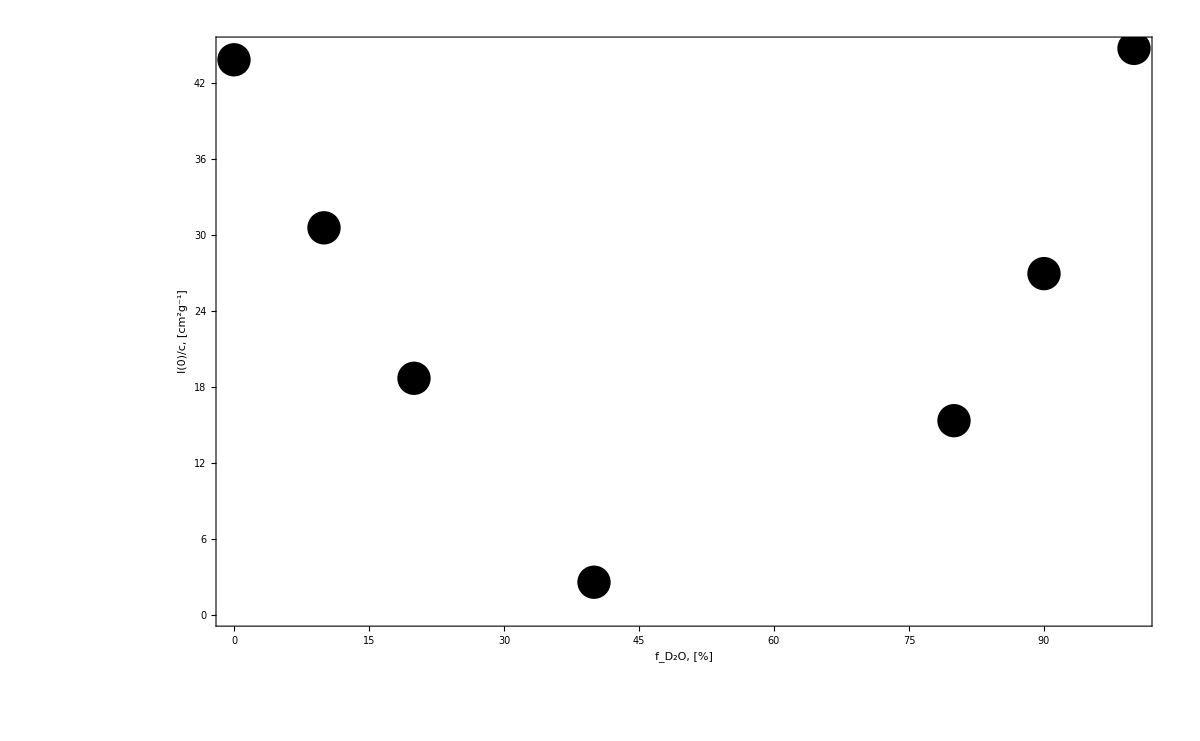

```mathematica
pointswitherrors=ErrorListPlot[pts,PlotStyle->{Black,PointSize[0.02],Thickness[.005]},Epilog->Inset[Style["h",56,Bold],{-10.9,45.5}],Axes->False,Frame->{{True,False},{True,False}},BaseStyle->{FontFamily->"Times New Roman",20},FrameStyle->Directive[Black,48,Thick],FrameLabel->{Row[{Subscript[Style["f",FontSlant->Italic], "D_2O"],", [%]"}],Row[{Style["I(0)/c",FontSlant->Italic], ", [cm^2g^-1]"}]},PlotRangeClipping->False,ImageSize->1200]
```

```mathematica
(*fitting data*)
```

```mathematica
nlm=NonlinearModelFit[pts⟦;;,1⟧,e+f x+g x^2,{e,f,g},x,Weights->1/errratio]
```

FittedModel[45.9112-1.79533 x+0.0177492 x^2]

```mathematica
(*find minimum*)
```

```mathematica
x/.Last[FindMinimum[nlm[x],{x,.5}]]
```

50.5749

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
e | 45.9112 | 1.43049 | 32.0948 | 5.61836×10^-6
f | -1.79533 | 0.0703927 | -25.5045 | 0.0000140361
g | 0.0177492 | 0.000636934 | 27.8667 | 9.86489×10^-6

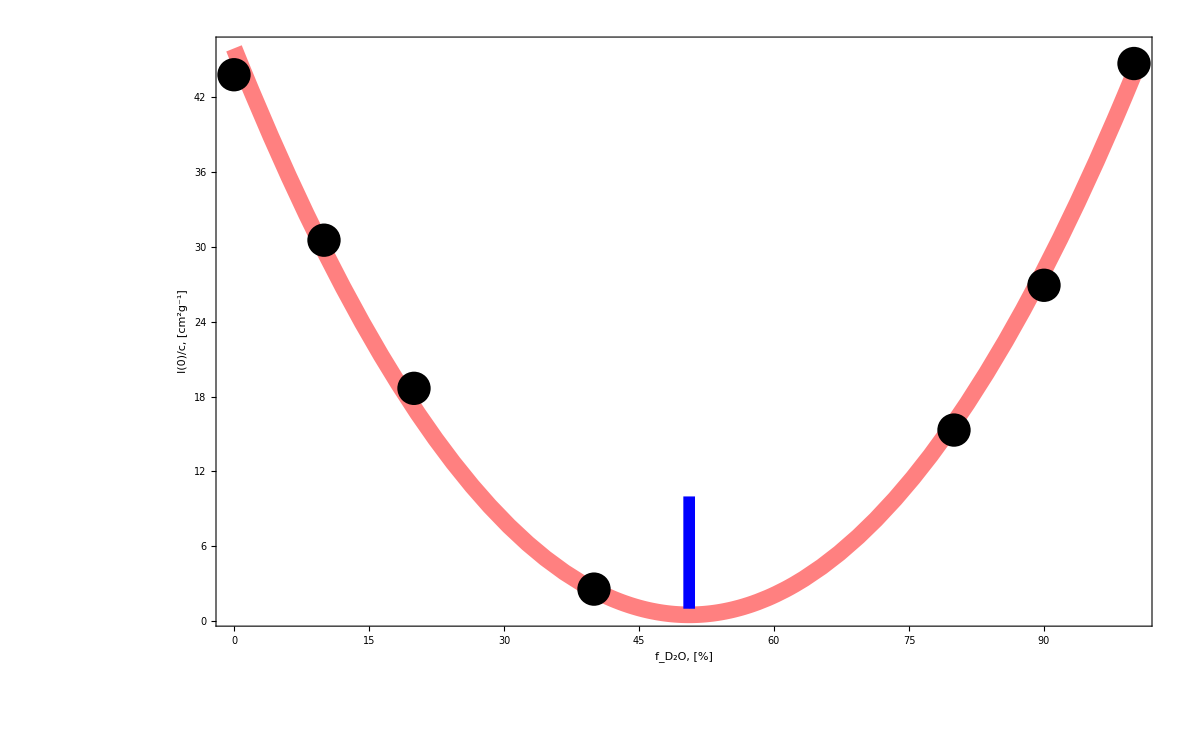

```mathematica
plt=Show[Plot[nlm[x],{x,0,100},PlotStyle->{Pink,Thickness[0.01]},PlotRange->All,Epilog->Inset[Style["h",56,Bold],{-12.9,46.5}],Axes->False,Frame->{{True,False},{True,False}},BaseStyle->{FontFamily->"Times New Roman",20},FrameStyle->Directive[Black,54,Thick],FrameLabel->{Row[{Subscript[Style["f",FontSlant->Italic], "D_2O"],", [%]"}],Row[{Style["I(0)/c",FontSlant->Italic], ", [cm^2g^-1]"}]},PlotRangeClipping->False,ImageSize->1200],pointswitherrors,Graphics[{Thickness[0.007],Blue,Arrow[{{x/.Last[FindMinimum[nlm[x],{x,.5}]],10},{x/.Last[FindMinimum[nlm[x],{x,.5}]],1}}]}]]
```

```mathematica
Export["fig5h.png",plt]
```

fig5h.png